```mathematica
(*for calculating sensitivity analysis of individual parameters*)
pathdirectory="C:\\Documents and Settings\\Hester_lab\\Desktop\\small-stoch-model\\"
path=pathdirectory;
pathdata=pathdirectory<>"\\Metropolis\\";
pathsvm=pathdirectory<>"\\svm_light_windows\\";
SetDirectory[pathdirectory];
SetDirectory[pathdata]
(*this subcode is for re-loading previously generated individuals*)
(*
BD=Import["C:\\Documents and Settings\\Hester_lab\\Desktop\\BleedDataBest.txt","List"];
BD=Map[ToExpression,BD];
Length[BD]
*)
```

C:\Documents and Settings\Hester_lab\Desktop\small-stoch-model\

C:\Documents and Settings\Hester_lab\Desktop\small-stoch-model\Metropolis

```mathematica
(*data entry*)
(*CISkillman={2.7,2.7,2.9,2.3,2.2,2.7,2.7,3.2,3.2,3.2,3.3,2.7,3,3.3,2.6,2.1}; (*check*)
CIEsten={3.01,3.45,3.69,2.96,2.63,3.44,2.74,3.08};
CIBolomey={4.29,3.44,3.43,3.49,4.68,5.03,3.38,3.7,4.53,3.44,3.45,3.02,4.69,3.81,7.42};
CIUlrych={6.23,4.04,3.37,5.24,4.48};
CIRakita={2.73,2.21,3.51,3.6,3.51,3.12,3.1};(*check*)
(*CIWeissler={2.81,2.9,3.00,2.94,2.83};*)
CIWeissler={3.5,2.5,3.2,2.9,2.4,2.7,2.2,3.8};(* check*)
CI=Join[CISkillman,CIBolomey,CIRakita,CIWeissler,CIUlrych];
COdata=CI*1.73*1000;

MAP={71,85,87,92,93,112,106,86,102,104,86};
TPRSkillman={1.372,1.285,1.369,1.737,1.679,1.758,1.569,1.342,1.346,1.079,1.076,1.468,1.305,1.33,1.6,1.881};
TPRBolomey={0.95,1.18,1.31,1.34,0.9,0.68,1.3,1.0,0.96,1.05,1.02,1.41,0.835,1.04,0.550};
TPREsten={1.41,1.28,1.25,1.61,1.62,1.16,1.08,1.77};
TPRUlrych={0.015,0.019,0.025,0.016,0.016};
TPRRakita={1.75,1.572,1.068,.96,.98,.975,.993};
(*TPRWeissler={1.189,.980,1.220,1.087,1.104};*)
TPRWeissler={1.128,1.302,1.125,1.108,1.407,1.358,1.132,1.064}
TPRdata=Join[Join[TPRSkillman,TPRBolomey,TPRRakita,TPRWeissler]/77.78,TPRUlrych];
*)
bvpop=RandomVariate[NormalDistribution[5,0.5],50];
ecfvpop=Table[(bvpop[[i]]-RandomVariate[NormalDistribution[1.5,0.5],1])*5,{i,1,Length[bvpop]}][[All,1]];
pop=Transpose[{bvpop,ecfvpop}]
SKdouble=SmoothKernelDistribution[pop,{"Standardized",0.5}];
PDdouble=PDF[SKdouble,{X,Y}];
Plot3D[PDdouble,{X,1,10},{Y,5,25},PlotRange->All]
SetDirectory[pathdata];
```

{{5.40611,20.7214},{4.22913,14.4092},{5.09309,18.1759},{4.89394,19.3905},{4.81158,18.2039},{4.86491,19.0085},{5.36852,17.8827},{5.11499,19.176},{4.76803,14.1153},{5.12215,14.4379},{5.08268,12.338},{5.68883,24.8453},{5.53686,19.8102},{5.01237,16.2002},{5.06572,18.1523},{5.06603,17.9452},{4.71513,14.1961},{5.42267,20.965},{4.99972,13.5232},{5.06922,18.5975},{5.19487,18.0067},{4.61104,13.626},{4.42702,12.5668},{4.10698,8.28024},{4.90946,17.6827},{4.30411,12.9521},{4.99215,16.2206},{4.93509,20.2694},{4.8332,17.7242},{4.86457,11.6308},{5.13665,20.5834},{5.80499,19.9506},{4.83163,15.3959},{4.0945,12.9371},{5.1098,16.7154},{4.66884,19.649},{5.56158,20.4746},{4.73869,13.6831},{5.81965,18.4588},{4.92423,16.0126},{5.58059,18.3578},{5.6838,20.499},{5.04193,22.3078},{6.07622,18.8832},{5.24068,14.4672},{4.58637,15.8557},{5.40061,23.2132},{4.40514,12.3833},{5.64283,17.5215},{5.29367,21.4809}}

-Graphics3D-

```mathematica
(*Given a parm list to be inserted into an ICS, this code accomplishes the insertion*)
(*Label the parm list as "Sample"*)

CreateICS:=Do[
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\Generate_ICS.Script </script></root> \" "];
,{1}]

CreateParmRoster:=Do[
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\GenerateRoster.Script </script></root> \" "];
SetDirectory[pathdata];
ParmList=Flatten[Drop[Import["InitialRoster.txt","CSV"],2],1];
ParmList=ToExpression[StringReplace[ParmList," "->""]],{1}];

CreateRoster:=Do[
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\GenerateShortRoster.Script </script></root> \" "];
SetDirectory[pathdata];
data1=Flatten[Drop[Import["CalibrationRoster.txt","CSV"],2],1];
RosterList=ToExpression[StringReplace[data1," "->""]];
ParmList=Drop[RosterList,13],{1}];

SensitivityAnalysis[level_]:=Do[
(*initialize running tables*)
Delta={};
Score={};
SetDirectory[pathdata];
data=Import["Stoch.ICS","Text"];
(*find normal CO*)
rsl="FluidVolumes.BV"<>" </name>\n<val>";
split=StringSplit[data,rsl->rsl<>" "];
split3=StringSplit[split[[3]],"</val>",2];
COval=ToExpression[split3[[1]]];
(*find normal TPR*)
rsl="FluidVolumes.ECFV"<>" </name>\n<val>";
split=StringSplit[data,rsl->rsl<>" "];
split3=StringSplit[split[[3]],"</val>",2];
TPRval=ToExpression[split3[[1]]];
(*cycles through all parameters; designates Delta[[i]] as 10% of the fitted value, uses base[[i]]+/- Delta[[i]] to compute sensitivity as baseline*)
For[j=1,j≤Length[ParmList],j++,
ParmName=StringReplace[ToString[ParmList[[j]]],{" "->"","("->"",")"->""}];
rsl=ParmName<>" </name>\n<val>";
split=StringSplit[data,rsl->rsl<>" "];
split3=StringSplit[split[[3]],"</val>",2];
oldval=ToExpression[split3[[1]]];
AppendTo[Delta,oldval/10];


newval=ToString[oldval*0.9]<>" </val>";
NewTail=newval<>split3[[2]];
data=split[[1]]<>split[[2]]<>NewTail;
Export["SensStoch.ICS",data,"Text"];
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\SensStoch.Script </script></root> \" "];
dataout1=ToExpression[StringInsert[StringDrop[StringInsert[Import[pathdata<>"SensOut.txt","List"][[1]],"{",1],-1],"}",-1]];

SetDirectory[pathdata];
newval=ToString[oldval*1.1]<>" </val>";
NewTail=newval<>split3[[2]];
data=split[[1]]<>split[[2]]<>NewTail;
Export["SensStoch.ICS",data,"Text"];
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\SensStoch.Script </script></root> \" "];
dataout2=ToExpression[StringInsert[StringDrop[StringInsert[Import[pathdata<>"SensOut.txt","List"][[1]],"{",1],-1],"}",-1]];
AppendTo[Score,Sqrt[Apply[Plus,(100*(dataout1-dataout2)/{COval,TPRval})^2]]]];
SA=Transpose[{ParmList,Score,N[Delta]}];
Sensitives=Select[SA,#[[2]]>level&];
Delta=Transpose[Sensitives][[-1]],{1}];


(*initializes running tables*)
InitializeProcess:=Do[
SetDirectory[pathdata];
data=Import["Stoch_bak.ICS","Text"];
Export["Stoch.ICS",data,"Text"];
BleedData={};
ParmDistributions={};
Fails={};
CollectedData={};
Bleed1={};
Coll1={};
probs={};
OutOfBounds={};
reseedcounter=0;
,{1}];

(*takes argument BigDelta for reseeding the start process*)
Restart[BDel_]:=Do[
SetDirectory[pathdata];
data=Import["Stoch_bak.ICS","Text"];
Export["Stoch.ICS",data,"Text"];
ModifyAllICS[BDel];
reseedcounter=0;
,{1}];

ModifyAllICS[set_]:=Do[
SetDirectory[pathdata];
data=Import["Stoch.ICS","Text"];
For[ii=1,ii≤Length[set],ii++,
Sample=RandomVariate[NormalDistribution[0,set[[ii]]]];
ParmEst=ToString[Sample];
ParmName=StringReplace[Map[ToString,Sensitives[[All,1]]],{" "->"","("->"",")"->""}][[ii]];
rsl=ParmName<>" </name>\n<val>";
split=StringSplit[data,rsl->rsl<>" "];
split3=StringSplit[split[[3]],"</val>",2];
oldval=ToExpression[split3[[1]]];
newval=" "<>ToString[oldval+Sample]<>" </val>";
If[ParmName=="BaroreceptorReflex.KBARO",AppendTo[valtracker,{ParmName,"  ",oldval,"  ",Sample,newval}]];
NewTail=newval<>split3[[2]];
data=split[[1]]<>split[[2]]<>NewTail;
Export["Stoch.ICS",data,"Text"]]
,{1}];

Reseed:=Do[
reseedcounter++;
If[(reseedcounter>10||Length[CollectedData]==0),Restart[BigDelta],
SetDirectory[pathdata];
dataR=Import["Stoch_bak.ICS","Text"];
u=RandomInteger[{1,Round[0.5*Length[CollectedData]]}];
Print["Reseed   ",u];
FullSample=Drop[CollectedData[[u]],3];
For[ii=1,ii≤Length[Delta],ii++,
Sample=RandomVariate[NormalDistribution[0,Delta[[ii]]]];
ParmEst=ToString[Sample];
ParmName=StringReplace[Map[ToString,Sensitives[[All,1]]],{" "->"","("->"",")"->""}][[ii]];
rsl=ParmName<>" </name>\n<val>";
split=StringSplit[dataR,rsl->rsl<>" "];
split3=StringSplit[split[[3]],"</val>",2];
oldval=ToExpression[split3[[1]]];
newval=ToString[FullSample[[ii]]+Sample]<>" </val>";
NewTail=newval<>split3[[2]];
dataR=split[[1]]<>split[[2]]<>NewTail];
Export["Stoch.ICS",dataR,"Text"]]
,{1}]

Bleed:=Do[
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\Bleed.Script </script></root> \" "];
SetDirectory[pathdata];
raw=Import["BleedData.txt","CSV"];
If[Length[raw]==5,
(*true*)AppendTo[BleedData,Transpose[Drop[Transpose[raw],-1]]],
(*false*)counter--]
,{1}];

Salt:=Do[
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\Salt.Script </script></root> \" "];
SetDirectory[pathdata];
raw=Import["SaltData.txt","CSV"];
If[Length[raw]==5,
(*true*)AppendTo[BleedData,Transpose[Drop[Transpose[raw],-1]]],
(*false*)counter--]
,{1}]

Calibrate[iindex_]:=Do[
counter=0;
p0=10^(-10);
While[counter<iindex,
SetDirectory[pathdata];
counter++;
If[IntegerQ[counter/25],Print[{counter/(25),Length[CollectedData],Length[Fails]}]];
ics=Import["Stoch.ICS","Text"];
ModifyAllICS[Delta];
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\Calibrate.Script </script></root> \" "];
SetDirectory[pathdata];
metdata=Drop[Import["Calibrate.txt","CSV"][[1]],-1];

p=PDF[SKdouble,{metdata[[2]],metdata[[11]]}];
If[condition[metdata],
p=PDF[SKdouble,{metdata[[2]],metdata[[11]]}],
p=0;
AppendTo[OutOfBounds,metdata]];
u=RandomReal[];
If[p/p0>=u,
Repcounter=0;
p0=p;
AppendTo[probs,p];
AppendTo[CollectedData,metdata],
Repcounter++;
counter--;
If[Or[metdata[[1]]==="N/A",Repcounter>10],
Reseed;
Repcounter=0,
AppendTo[Fails,p];
Export["Stoch.ICS",ics,"Text"]]]],{1}];

Validate[iindex_]:=Do[
valtracker={};
counter=0;
p0=10^(-10);
While[counter<iindex,
SetDirectory[pathdata];
counter++;
If[IntegerQ[counter/5],Print[{counter/5,Length[BleedData],Length[Fails]}]];
ics=Import["Stoch.ICS","Text"];
ModifyAllICS[Delta];
SetDirectory[path];
Run["scriptedcontroller \"<root><script> Metropolis\\Calibrate.Script </script></root> \" "];
SetDirectory[pathdata];
metdata=Drop[Import["Calibrate.txt","CSV"][[1]],-1];
p=PDF[SKdouble,{metdata[[2]],metdata[[11]]}];
If[condition[metdata],
p=PDF[SKdouble,{metdata[[2]],metdata[[11]]}],
p=0;
AppendTo[OutOfBounds,metdata]];
u=RandomReal[];
Print[counter," ",p0," ",p," ",p/p0," ",u];
If[p/p0>=u,
Repcounter=0;
p0=p;
AppendTo[probs,p];
Salt,
Repcounter++;
counter--;
AppendTo[Fails,p];
If[Or[metdata[[1]]==="N/A",Repcounter>10],
Reseed;
Repcounter=0,
Export["Stoch.ICS",ics,"Text"]]]]
,{1}]

WrapUp:=Do[
Bleed1=Flatten[AppendTo[Bleed1,BleedData],1];
Coll1=Flatten[AppendTo[Coll1,CollectedData],1];
DistData=Flatten[Bleed1,1][[All,1]],{1}];

condition[x_]:=And[3000<x[[2]]<9000,-5<x[[3]]<10,0<x[[4]]<15,60<x[[6]],2000<x[[7]]<7000,10000<x[[8]]<20000,x[[19]]>0]
```

```mathematica
(*Reopen from existing save files*)
CreateParmRoster;
CreateRoster;
```

```mathematica
(*Full initialize*)
CreateICS;
CreateParmRoster;
(*SensitivityAnalysis[5];*)
```

```mathematica
(*restart*)
CreateICS;
CreateParmRoster;
CreateRoster;
InitializeProcess;
bar=Delta/2
BigDelta=Delta*2;
Sensitives[[All,1]]
```

{256.3,0.105,0.051,0.057}

{FlowAutoregulation.AutoS,BaroreceptorReflex.AffNaA,BaroreceptorReflex.SympsA,BaroreceptorReflex.SympsB}

BleedData

{{CardiacOutput.V0,0.366479,333.},{CardiacOutput.slope_a,1.62228,0.0344},{CardiacOutput.slope_b,0.540355,0.0649},{FluidVolumes.Intake,0.76676,0.1},{FlowAutoregulation.KAUTO,0.833393,0.000048},{BaroreceptorReflex.KBARO,2.56341,0.00007},{CardiacOutput.StarlingA,0.340701,750.},{CardiacOutput.Starlingm,2.13637,0.1876},{CardiacOutput.StarlingS,0.254371,0.285},{FluidVolumes.FluidA,2.61058,790.},{FluidVolumes.Fluidm,2.60159,0.358},{FluidVolumes.FluidS,0.219839,1557.},{FluidVolumes.Urinem,0.624497,0.005},{FlowAutoregulation.AutoA,0.899295,0.00453},{FlowAutoregulation.Autom,4.23165,1.086},{FlowAutoregulation.AutoS,8.01219,512.6},{BaroreceptorReflex.AffNaA,6.71116,0.21},{BaroreceptorReflex.AffNam,3.93448,0.363},{BaroreceptorReflex.AffNaS,3.39826,5.},{BaroreceptorReflex.SympsA,7.61118,0.102},{BaroreceptorReflex.Sympsm,3.51231,0.349},{BaroreceptorReflex.SympsS,4.219,0.053},{BaroreceptorReflex.SympsB,5.55798,0.114},{CardiacOutput.RVRa,1.27866,0.0035},{CardiacOutput.RVRb,0.395904,0.000064}}

```mathematica
(*here*)
calnumber=1;
valnumber=1;
NumberBatches=1;
Do[
Restart[BigDelta];
Repcounter=0;
Calibrate[calnumber];
Print["begin validate"];
Validate[valnumber];
AppendTo[ParmDistributions,Drop[CollectedData,Round[calnumber/2]]],{NumberBatches}]

Roster=Flatten[Drop[Import[pathdata<>"BleedRoster.txt","CSV"],2]];

AcceptanceRate=N[Length[Fails]/(Length[Fails]+Length[CollectedData]+Length[BleedData])]
```

$Aborted

1.

```mathematica
CollectedData
BleedData
```

{}

{}

```mathematica
BD=BleedData;
(*Roster=Flatten[Drop[Import[pathdata<>"BleedRoster.txt","CSV"],2]];*)
Length[BD]
BleedData=BD;
AugmentedBD=Transpose[Join[Prepend[Transpose[BD[[All,5]]],BleedData[[All,1]][[All,6]]-BleedData[[All,5]][[All,6]]],Take[Drop[Transpose[BD[[All,1]]],1],12]]];
AugmentedBD0=Transpose[Prepend[Transpose[BD[[All,1]]],BleedData[[All,1]][[All,6]]-BleedData[[All,5]][[All,6]]]];
AugmentedBD[[1]]
BleedRoster=Join[{"Delta MAP"},Join[Roster,Take[Roster,{2,13}]]]
BleedRoster0=Join[{"Delta MAP"},Roster]
Compensators=Select[AugmentedBD0,#[[1]]<=15&];
DeCompensators=Select[AugmentedBD0,#[[1]]>15&];
Length[Compensators]
Length[DeCompensators]
N[Length[Compensators]/(Length[DeCompensators]+Length[Compensators])]
```

300

{2.3,576020.,5046.91,-1.434,5.269,0.008137,98.4,3977.6,14479.9,98.362,0.615,0.01949,0.649,1.488,3330,0.344,0.649,1.,0.00048,0.00079,7500.,1.9,2.9,9404.38,4.28,15570.,0.05,0.045,10.86,7229.48,3.238,10.318,50.,1.498,6.907,0.527,1.201,0.035,0.00064,6700.61,0.826,8.598,0.007495,100.7,4477.2,15225.5,100.713,0.845,0.01503,0.963,1.224}

{Delta MAP,  System.X,  CardiacOutput.CO,  CardiacOutput.RAP,  CardiacOutput.MCFP,  CardiacOutput.Slope,  FluidVolumes.AP,  FluidVolumes.BV,  FluidVolumes.ECFV,  FluidVolumes.RPP,  FluidVolumes.UO,  FlowAutoregulation.TPR,  BaroreceptorReflex.AFFNA,  BaroreceptorReflex.SYMEnd,  CardiacOutput.V0,  CardiacOutput.slope_a,  CardiacOutput.slope_b,  FluidVolumes.Intake,  FlowAutoregulation.KAUTO,  BaroreceptorReflex.KBARO,  CardiacOutput.StarlingA,  CardiacOutput.Starlingm,  CardiacOutput.StarlingS,  FluidVolumes.FluidA,  FluidVolumes.Fluidm,  FluidVolumes.FluidS,  FluidVolumes.Urinem,  FlowAutoregulation.AutoA,  FlowAutoregulation.Autom,  FlowAutoregulation.AutoS,  BaroreceptorReflex.AffNaA,  BaroreceptorReflex.AffNam,  BaroreceptorReflex.AffNaS,  BaroreceptorReflex.SympsA,  BaroreceptorReflex.Sympsm,  BaroreceptorReflex.SympsS,  BaroreceptorReflex.SympsB,  CardiacOutput.RVRa,  CardiacOutput.RVRb,  CardiacOutput.CO,  CardiacOutput.RAP,  CardiacOutput.MCFP,  CardiacOutput.Slope,  FluidVolumes.AP,  FluidVolumes.BV,  FluidVolumes.ECFV,  FluidVolumes.RPP,  FluidVolumes.UO,  FlowAutoregulation.TPR,  BaroreceptorReflex.AFFNA,  BaroreceptorReflex.SYMEnd}

{Delta MAP,  System.X,  CardiacOutput.CO,  CardiacOutput.RAP,  CardiacOutput.MCFP,  CardiacOutput.Slope,  FluidVolumes.AP,  FluidVolumes.BV,  FluidVolumes.ECFV,  FluidVolumes.RPP,  FluidVolumes.UO,  FlowAutoregulation.TPR,  BaroreceptorReflex.AFFNA,  BaroreceptorReflex.SYMEnd,  CardiacOutput.V0,  CardiacOutput.slope_a,  CardiacOutput.slope_b,  FluidVolumes.Intake,  FlowAutoregulation.KAUTO,  BaroreceptorReflex.KBARO,  CardiacOutput.StarlingA,  CardiacOutput.Starlingm,  CardiacOutput.StarlingS,  FluidVolumes.FluidA,  FluidVolumes.Fluidm,  FluidVolumes.FluidS,  FluidVolumes.Urinem,  FlowAutoregulation.AutoA,  FlowAutoregulation.Autom,  FlowAutoregulation.AutoS,  BaroreceptorReflex.AffNaA,  BaroreceptorReflex.AffNam,  BaroreceptorReflex.AffNaS,  BaroreceptorReflex.SympsA,  BaroreceptorReflex.Sympsm,  BaroreceptorReflex.SympsS,  BaroreceptorReflex.SympsB,  CardiacOutput.RVRa,  CardiacOutput.RVRb}

129

171

0.43

```mathematica
(*BleedData=Transpose[ToExpression[BleedData]];*)
Outputs=BleedData[[All,1,{2,11}]];
singleObj=SmoothHistogram3D[Transpose[{COdata,TPRdata}],PlotRange->{{3000,9000},{0.005,0.025}},ColorFunction->"SouthwestColors",ViewPoint->{-2,2.,4},PlotRange->All,Axes->{True,True,False},AxesLabel->{"CO","TPR"}]
SmoothHistogram3D[Outputs,PlotRange->{{3000,9000},{0.005,0.025}},ColorFunction->"RustTones"]
doubleObj=Show[SmoothHistogram3D[Transpose[{COdata,TPRdata}],PlotRange->{{3000,9000},{0.005,0.025}},ColorFunction->"SouthwestColors"],
SmoothHistogram3D[Outputs,PlotRange->{{3000,9000},{0.005,0.025}},ColorFunction->"RustTones"],ViewPoint->{-2,-3.5,4},PlotRange->All,Axes->{True,True,False},AxesLabel->{"CO","TPR"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

C:\Documents and Settings\Hester_lab\Desktop\Integrated_Calibration\Metropolis\single.bmp

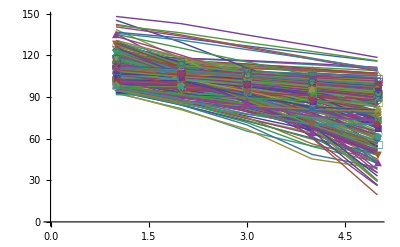

Deltas

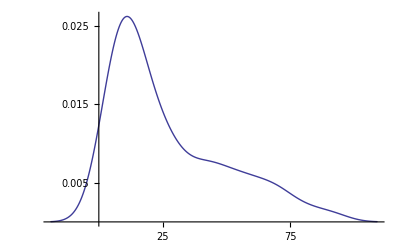

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Pressures=BD[[All,All,6]];
Volumes=BD[[All,All,7]];
ListPlot[Pressures,Joined->True,Mesh->All,PlotMarkers->Automatic]
Deltas=Table[Pressures[[i,1]]-Pressures[[i,-1]],{i,1,Length[Pressures]}];
DeltaI=Table[Pressures[[i,1]]-Pressures[[i,j]],{i,1,Length[Pressures]},{j,1,5}];
DeltaSign=Table[If[Pressures[[i,1]]-Pressures[[i,j]]≤15,1,-1],{i,1,Length[Pressures]},{j,1,5}];

Print["Deltas"]
SmoothHistogram[Deltas]
N[Length[Select[Deltas,#<15&]]/Length[BleedData]]
```

```mathematica
(*this begins the SVM portion of the program*)
AugmentedBD0Reverse=Transpose[Drop[Append[Transpose[AugmentedBD0],AugmentedBD[[All,1]]],1]];
AppendedBleedData=Table[Transpose[Join[Transpose[BD[[i]]],{DeltaSign[[i]]}]],{i,1,Length[BleedData]}];
F[x_]:=If[Chop[StandardDeviation[x]]==0,Table[1,{Length[x]}],Table[1+(x[[i]]-Min[x])/(Max[x]-Min[x]),{i,1,Length[x]}]]
NormalizedBleedData=Transpose[Map[F,Transpose[BD[[All,1]]]]];
BleedDataForSVM=Transpose[Join[Transpose[NormalizedBleedData],{Transpose[DeltaSign][[-1]]}]];
VaryingComponents=Take[Drop[Union[Table[If[Map[Length[Union[#]]&,Transpose[BD[[All,1]]]][[j]]>1,j,0],{j,1,Length[Roster]}]],1],-10]
SetDirectory[pathdata]
Export["Middle.xls",Transpose[AppendedBleedData]]
Export[pathdata<>"Middle.CSV",BleedDataForSVM]
```

Middle.xls

C:\Documents and Settings\Hester_lab\Desktop\Integrated_Calibration\Metropolis\Middle.CSV

C:\Documents and Settings\Hester_lab\Desktop\Integrated_Calibration

{1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,1,1,-1,1,-1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,1,-1,1,1,1,1,-1,-1,1,-1,1,1,1,1,1,1,-1,-1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,1,-1,1,1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1,-1,-1,1}

{0.923129,0.00963024}

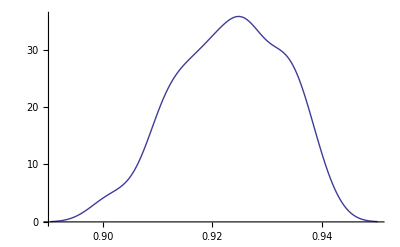

1.5

0.

```mathematica
(*Close[FileNameJoin[{path,"SVM_full.txt"}]]*)

data=Import[pathdata<>"Middle.CSV"];
SetDirectory[pathsvm];
DL=Length[data];
NL=Length[data[[1]]];
FullList=data[[All,1;;NL]];
FullList[[All,-1]]
BETA={};
ShortPerformance={};
Do[
NN=225;
Select100=Sort[RandomSample[Range[DL],NN]];
SL=data[[All,-1]];
MI=NL-1;
FLTr=FullList[[Select100]];
Deselect100=Complement[Range[Length[FullList]],Select100];
FLTe=FullList[[Deselect100]];
set=FLTr;

str=OpenWrite[FileNameJoin[{path,"SVM_train.txt"}]];
For[ii=1,ii≤NN,ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
WriteString[str,eleOut<>"\n"]];
Close[str];

set=FullList;
str1=OpenWrite[FileNameJoin[{path,"SVM_full.txt"}]];
LL=Length[set];
For[ii=1,ii≤LL,ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
WriteString[str1,eleOut<>"\n"]];

Close[str1];

SetDirectory[pathsvm];
beta=1.5;
(*beta=RandomVariate[UniformDistribution[{1,3}]];*)
AppendTo[BETA,beta];
beta=ToString[beta];
Run["SVMLEARNmathematica.bat "<>beta];
pred=Import["prediction.txt","Text"];
pred=ToExpression[StringInsert[StringInsert[StringReplace[pred,"\n"->","],"{",1],"}",-1]];
SP=Sign[pred];

Percent=N[Count[SP*SL,1]/Length[SP]];
AppendTo[ShortPerformance,Percent],{98}]
{Mean[ShortPerformance],StandardDeviation[ShortPerformance]}
SmoothHistogram[ShortPerformance]
Mean[BETA]
StandardDeviation[BETA]
```

```mathematica
mbs=Mean[ShortPerformance]
vbs=StandardDeviation[ShortPerformance]
Print["CI = [",mbs-1.96*vbs/Sqrt[Length[ShortPerformance]],",",mbs+1.96*vbs/Sqrt[Length[ShortPerformance]],"]"];
```

0.923129

0.00963024

CI = [0.921223,0.925036]

```mathematica
ClearAll[MER]
SetDirectory[path]
data=Import[pathdata<>"Middle.CSV"];
SetDirectory[pathsvm];
DL=Length[data];
NL=Length[data[[1]]];
FullList=data[[All,1;;NL]];
FullList[[All,-1]]
VaryingComponents=Drop[Union[Table[If[Map[Length[Union[#]]&,Transpose[BD[[All,1]]]][[j]]>1,j,0],{j,1,Length[Roster]}]],1];
MER:=Do[
NN=250;
vc=RandomSample[Take[VaryingComponents]];
AugmentSet[X_]:=Flatten[Table[Map[Union[X[[jin]],#]&,Subsets[Complement[vc,X[[jin]]],{1}]],{jin,1,Length[X]}],1];
data=Import[pathdata<>"Middle.CSV"];
SetDirectory[pathsvm];
DL=Length[data];
NL=Length[data[[1]]];
FullList=data[[All,1;;NL]];
Select100=Sort[RandomSample[Range[DL],NN]];
SL=data[[All,-1]];
BestPercent=0;
Best={N[Max[Count[SL,1],Count[SL,-1]]/Length[SL]]};
GoodSets={{}};
Seed={{NL}};
cntr=0;
PCav=N[Max[Count[SL,1],Count[SL,-1]]/Length[SL]];

While[Seed≠{},
cntr++;
PCList={};
PrevBest=Max[PCav];
Test=AugmentSet[Seed];
Success={};
For[index=1,index≤Length[Test],index++,
FullList=data[[All,Test[[index]]]];
MI=Length[FullList[[1]]]-1;
FLTr=FullList[[Select100]];
Deselect100=Complement[Range[Length[FullList]],Select100];
FLTe=FullList[[Deselect100]];
set=FLTr;

str=OpenWrite[FileNameJoin[{path,"SVM_train.txt"}]];
For[ii=1,ii≤NN,ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
WriteString[str,eleOut<>"\n"]];
Close[str];

set=FullList;
strfull=OpenWrite[FileNameJoin[{path,"SVM_full.txt"}]];
LL=Length[set];
For[ii=1,ii≤LL,ii++,
ele=set[[ii]];
ele1=ele;
FTable=Reverse[Table[index,{index,1,MI}]];
Do[
ele1=ReplacePart[ele1,FTable[[MI+1-i]]->ToString[{FTable[[i]],":",ele[[i]],"x"}]],{i,1,MI}];
ele1=Reverse[ele1];
ele1=ReplacePart[ele1,1->{ele1[[1]],"x"}];
ele1=ToString[ele1];
eleOut=StringReplace[ele1,{{"{","}",","}->""," "->"","x"->" "}];
WriteString[strfull,eleOut<>"\n"]];
Close[strfull];

SetDirectory[pathsvm];
Run["SVMLEARNmathematica.bat"<>" 2 "];

pred=Import["prediction.txt","Text"];
pred=ToExpression[StringInsert[StringInsert[StringReplace[pred,"\n"->","],"{",1],"}",-1]];
SP=Sign[pred];
Percent=N[Count[SP*SL,1]/Length[SP]];
If[Percent>PrevBest+0.025,AppendTo[GoodSets,Test[[index]]];AppendTo[Success,Test[[index]]];AppendTo[PCList,Percent]];
If[Percent>BestPercent,
BestPercent=Percent;
Best=Test[[index]]]];
Seed=Success;
PCav=Mean[{BestPercent,Mean[PCList]}]];
AppendTo[BestSet,BestPercent];
Print[extcntr,"  Best is ",Best," and BestPercent is ",BestPercent];
extcntr++,{1}]

VarDistribution={};
BestSet={};
Do[
extcntr=1;
MER;
AppendTo[VarDistribution,Best],{100}]
varout=Sort[Flatten[VarDistribution]];
counttable=Table[Count[varout,VaryingComponents[[j]]],{j,1,Length[VaryingComponents]}]
Sensitives[[All,1]]
```

C:\Documents and Settings\Hester_lab\Desktop\Integrated_Calibration

{1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,1,1,-1,1,-1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,1,-1,1,1,1,1,-1,-1,1,-1,1,1,1,1,1,1,-1,-1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,1,-1,1,1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1,-1,-1,1}

1  Best is {3,19,23,33,35,39} and BestPercent is 0.923333

1  Best is {3,8,23,29,33,39} and BestPercent is 0.916667

1  Best is {3,6,23,33,35,39} and BestPercent is 0.92

1  Best is {2,3,6,23,33,39} and BestPercent is 0.92

1  Best is {2,3,23,33,35,39} and BestPercent is 0.913333

1  Best is {3,12,23,33,34,39} and BestPercent is 0.92

1  Best is {3,13,23,29,33,39} and BestPercent is 0.923333

1  Best is {3,6,10,19,23,33,39} and BestPercent is 0.93

1  Best is {3,5,23,33,35,39} and BestPercent is 0.923333

1  Best is {3,13,19,23,33,39} and BestPercent is 0.92

1  Best is {3,6,23,29,33,39} and BestPercent is 0.92

1  Best is {3,23,29,33,36,39} and BestPercent is 0.916667

1  Best is {3,12,23,29,33,39} and BestPercent is 0.916667

1  Best is {3,19,23,33,34,39} and BestPercent is 0.92

1  Best is {2,3,23,24,33,39} and BestPercent is 0.916667

1  Best is {3,5,23,29,33,39} and BestPercent is 0.916667

1  Best is {2,3,23,33,36,39} and BestPercent is 0.92

1  Best is {3,12,23,29,33,39} and BestPercent is 0.92

1  Best is {3,5,23,29,33,39} and BestPercent is 0.926667

1  Best is {2,3,23,33,36,39} and BestPercent is 0.923333

1  Best is {3,6,23,33,35,39} and BestPercent is 0.92

1  Best is {3,19,23,33,34,35,39} and BestPercent is 0.933333

1  Best is {3,10,19,23,33,34,39} and BestPercent is 0.933333

1  Best is {2,3,5,23,33,39} and BestPercent is 0.923333

1  Best is {2,3,5,23,33,39} and BestPercent is 0.92

1  Best is {3,23,24,33,35,39} and BestPercent is 0.916667

1  Best is {6,7,19,23,33,39} and BestPercent is 0.916667

1  Best is {2,3,5,23,33,39} and BestPercent is 0.92

1  Best is {7,19,23,33,39} and BestPercent is 0.913333

1  Best is {3,6,7,23,33,35,39} and BestPercent is 0.926667

1  Best is {2,3,5,23,33,39} and BestPercent is 0.916667

1  Best is {3,6,23,33,35,39} and BestPercent is 0.92

1  Best is {3,6,23,33,35,39} and BestPercent is 0.92

1  Best is {3,11,19,23,33,39} and BestPercent is 0.916667

1  Best is {3,10,19,23,33,39} and BestPercent is 0.926667

1  Best is {3,6,23,33,35,39} and BestPercent is 0.92

1  Best is {3,11,19,23,33,39} and BestPercent is 0.92

$Aborted

{9,35,0,7,10,3,1,0,3,2,3,2,11,37,2,8,0,0,37,4,11,3}

{BaroreceptorReflex.KBARO,FluidVolumes.FluidA,FluidVolumes.Fluidm,FlowAutoregulation.AutoS,BaroreceptorReflex.AffNaA,BaroreceptorReflex.AffNam,BaroreceptorReflex.SympsA,BaroreceptorReflex.Sympsm,BaroreceptorReflex.SympsS,BaroreceptorReflex.SympsB}

C:\Documents and Settings\Hester_lab\Desktop\Integrated_Calibration\SVM_full.txt

```mathematica
VaryingComponents=Take[Drop[Union[Table[If[Map[Length[Union[#]]&,Transpose[BD[[All,1]]]][[j]]>1,j,0],{j,1,Length[Roster]}]],1],-10]
Drop[Union[Table[If[Map[Length[Union[#]]&,Transpose[BD[[All,1]]]][[j]]>1,j,0],{j,1,Length[Roster]}]],1]
```

{19,23,24,29,30,31,33,34,35,36}

{2,3,4,5,6,7,8,9,10,11,12,13,19,23,24,29,30,31,33,34,35,36}

```mathematica
Roster[[VaryingComponents]]
Length[BestSet]
mbs=Mean[BestSet]
vbs=StandardDeviation[BestSet]
Print["CI = [",mbs-1.96*vbs/Sqrt[Length[BestSet]],",",mbs+1.96*vbs/Sqrt[Length[BestSet]],"]"];
fordisplay=Transpose[{Roster[[VaryingComponents]],N[counttable]}]
fordisplay=Sort[fordisplay,#1[[2]]<=#2[[2]]&]
TableForm[fordisplay]
N[Apply[Plus,counttable]/Length[BestSet]]
```

{  CardiacOutput.CO,  CardiacOutput.RAP,  CardiacOutput.MCFP,  CardiacOutput.Slope,  FluidVolumes.AP,  FluidVolumes.BV,  FluidVolumes.ECFV,  FluidVolumes.RPP,  FluidVolumes.UO,  FlowAutoregulation.TPR,  BaroreceptorReflex.AFFNA,  BaroreceptorReflex.SYMEnd,  BaroreceptorReflex.KBARO,  FluidVolumes.FluidA,  FluidVolumes.Fluidm,  FlowAutoregulation.AutoS,  BaroreceptorReflex.AffNaA,  BaroreceptorReflex.AffNam,  BaroreceptorReflex.SympsA,  BaroreceptorReflex.Sympsm,  BaroreceptorReflex.SympsS,  BaroreceptorReflex.SympsB}

37

0.920811

0.00474051

CI = [0.919283,0.922338]

{{  CardiacOutput.CO,9.},{  CardiacOutput.RAP,35.},{  CardiacOutput.MCFP,0.},{  CardiacOutput.Slope,7.},{  FluidVolumes.AP,10.},{  FluidVolumes.BV,3.},{  FluidVolumes.ECFV,1.},{  FluidVolumes.RPP,0.},{  FluidVolumes.UO,3.},{  FlowAutoregulation.TPR,2.},{  BaroreceptorReflex.AFFNA,3.},{  BaroreceptorReflex.SYMEnd,2.},{  BaroreceptorReflex.KBARO,11.},{  FluidVolumes.FluidA,37.},{  FluidVolumes.Fluidm,2.},{  FlowAutoregulation.AutoS,8.},{  BaroreceptorReflex.AffNaA,0.},{  BaroreceptorReflex.AffNam,0.},{  BaroreceptorReflex.SympsA,37.},{  BaroreceptorReflex.Sympsm,4.},{  BaroreceptorReflex.SympsS,11.},{  BaroreceptorReflex.SympsB,3.}}

{{  CardiacOutput.MCFP,0.},{  FluidVolumes.RPP,0.},{  BaroreceptorReflex.AffNaA,0.},{  BaroreceptorReflex.AffNam,0.},{  FluidVolumes.ECFV,1.},{  FlowAutoregulation.TPR,2.},{  BaroreceptorReflex.SYMEnd,2.},{  FluidVolumes.Fluidm,2.},{  FluidVolumes.BV,3.},{  FluidVolumes.UO,3.},{  BaroreceptorReflex.AFFNA,3.},{  BaroreceptorReflex.SympsB,3.},{  BaroreceptorReflex.Sympsm,4.},{  CardiacOutput.Slope,7.},{  FlowAutoregulation.AutoS,8.},{  CardiacOutput.CO,9.},{  FluidVolumes.AP,10.},{  BaroreceptorReflex.KBARO,11.},{  BaroreceptorReflex.SympsS,11.},{  CardiacOutput.RAP,35.},{  FluidVolumes.FluidA,37.},{  BaroreceptorReflex.SympsA,37.}}

CardiacOutput.MCFP | 0.
  FluidVolumes.RPP | 0.
  BaroreceptorReflex.AffNaA | 0.
  BaroreceptorReflex.AffNam | 0.
  FluidVolumes.ECFV | 1.
  FlowAutoregulation.TPR | 2.
  BaroreceptorReflex.SYMEnd | 2.
  FluidVolumes.Fluidm | 2.
  FluidVolumes.BV | 3.
  FluidVolumes.UO | 3.
  BaroreceptorReflex.AFFNA | 3.
  BaroreceptorReflex.SympsB | 3.
  BaroreceptorReflex.Sympsm | 4.
  CardiacOutput.Slope | 7.
  FlowAutoregulation.AutoS | 8.
  CardiacOutput.CO | 9.
  FluidVolumes.AP | 10.
  BaroreceptorReflex.KBARO | 11.
  BaroreceptorReflex.SympsS | 11.
  CardiacOutput.RAP | 35.
  FluidVolumes.FluidA | 37.
  BaroreceptorReflex.SympsA | 37.

5.08108

```mathematica
(*Begin PCA poprtion*)
PCAList=Join[Compensators,DeCompensators];
DeCompensators[[1]]
ZScore[a_]:=If[StandardDeviation[a]>0,Table[(a[[i]]-Mean[a])/StandardDeviation[a],{i,1,Length[a]}],Table[0,{Length[a]}]];

NormalizedPCAList=Transpose[Map[ZScore[#]&,Transpose[PCAList]]];
LimitBleedRoster=BleedRoster;
(*SingularValueDecomposition[PCAList][[1]]*)
```

{19.5,576000.,4678.53,-1.764,5.218,0.008413,113.9,3950.2,14068.,113.91,1.055,0.02435,2.536,1.607,3330,0.344,0.649,1.,0.00048,0.00091,7500.,1.9,2.9,9479.61,3.315,15570.,0.05,0.045,10.86,4913.98,4.446,5.414,50.,2.237,6.165,0.354,1.607,0.035,0.00064}

{{-1.09602,0,0.569915,0.44127,0.467076,-0.450662,-0.790972,0.480961,0.580108,-0.789703,-1.38222,-1.05654,-0.286849,-0.452395,0,0,0,0,-0.998332,-0.0861668,0,0,0,-0.550674,0.245246,0,0,0,0,0.436312,0.578821,3.34146,0,0.745363,1.88597,-0.00351943,0.0022352,0,0},«298»,{-0.398508,0,0.227798,-0.30352,-0.186658,-0.0515664,0.0340108,-0.206944,0.952716,«22»,-0.721614,0,-0.276659,-1.29053,1.39076,-0.296864,0,0}}

```mathematica
(*TableForm[Covariance[NormalizedPCAList]]*)
Eigensystem[NormalizedPCAList]
```

Eigensystem::matsq: Argument {{-1.09602, 0, 0.569915, 0.44127, 0.467076, -0.450662, -0.790972, 0.480961, 0.580108, -0.789703, -1.38222, -1.05654, -0.286849, -0.452395, 0, 0, 0, 0, -0.998332, -0.0861668, 0, 0, 0, -0.550674, 0.245246, 0, 0, 0, 0, 0.436312, 0.578821, 3.34146, 0, 0.745363, 1.88597, -0.00351943, 0.0022352, 0, 0}, « 49 », « 250 »} at position 1 is not a non-empty square matrix.

Eigensystem[{{-1.09602,0,0.569915,0.44127,0.467076,-0.450662,-0.790972,0.480961,0.580108,-0.789703,-1.38222,-1.05654,-0.286849,-0.452395,0,0,0,0,-0.998332,-0.0861668,0,0,0,-0.550674,0.245246,0,0,0,0,0.436312,0.578821,3.34146,0,0.745363,1.88597,-0.00351943,0.0022352,0,0},{«1»},«297»,{-0.398508,0,0.227798,-0.30352,-0.186658,-0.0515664,0.0340108,-0.206944,«23»,-0.721614,0,-0.276659,-1.29053,1.39076,-0.296864,0,0}}]

```mathematica
Eigensystem[Covariance[NormalizedPCAList]][[1]]
PCA[num_]:=Take[Eigenvectors[Covariance[NormalizedPCAList]],num]
PCA[1].Transpose[NormalizedPCAList]
```

{7.21855,4.35414,2.43465,1.75249,1.66547,1.5611,1.21299,0.907865,0.676887,0.357398,0.326381,0.253607,0.120374,0.0579156,0.044635,0.0242688,0.0186468,0.00682145,0.0050807,0.000510645,0.000179865,0.000033904,3.39207×10^-6,-3.55491×10^-16,-1.64481×10^-16,7.82964×10^-17,-7.52711×10^-17,1.9082×10^-17,-5.89697×10^-18,5.72835×10^-19,3.26725×10^-19,3.2482×10^-19,2.92323×10^-19,3.35716×10^-20,2.10773×10^-20,3.09117×10^-21,0.,0.,0.}

{{1.86798,2.62409,3.01467,3.23655,3.75628,3.07923,2.88078,-1.18988,0.208183,0.963734,2.01132,2.96693,2.42021,2.84067,2.65746,1.28378,1.27037,1.29178,1.05341,0.529709,-0.509507,-0.447739,0.0582412,-0.70401,-0.815475,1.85265,1.47141,-0.40237,0.575811,2.37378,2.97578,3.09182,0.605389,-1.34543,-1.54659,-1.90292,-1.55275,-0.84994,-1.87077,-2.22004,-2.15619,-1.86272,-1.90534,-0.449979,2.85804,2.65955,3.99603,1.19841,0.917709,1.71561,1.69979,4.09225,2.51519,2.4473,3.13099,4.35199,3.19201,2.51762,3.17608,3.16516,3.02438,3.715,3.91708,4.30834,5.39747,3.66832,5.44167,5.91564,5.06432,4.61829,4.67693,5.52439,3.04659,1.79817,0.269354,4.3327,3.98908,1.80083,3.14509,1.75035,2.70251,3.47286,3.24814,3.75429,2.09853,1.43385,3.7305,1.49724,1.15792,1.29634,0.184979,0.0387152,-0.94158,0.573032,0.0822818,0.935855,1.78579,1.25121,1.35546,1.26959,-0.0109244,-0.225372,0.578483,2.29787,1.9041,1.14771,1.39238,3.06436,0.559752,-0.984345,-0.317472,-0.253044,-2.38904,1.36476,0.984669,0.557352,0.286321,0.505739,0.878212,2.06021,0.37328,-0.224306,-0.209714,-1.10008,-0.759273,-0.441685,-0.573474,-0.711971,0.313877,-0.515246,1.54209,-1.43395,-1.65765,-1.46149,-2.15121,-2.76138,-2.86351,-3.06852,-4.00008,-5.23285,-3.82493,-3.18808,-1.84767,-1.51556,-1.23122,-2.21864,-2.43927,-1.48502,-1.75526,-2.1128,-2.43135,-1.93856,-1.78836,-0.702907,-0.911214,-1.58426,-1.34549,-1.70023,-1.02404,-1.85479,-1.70587,-1.96204,-1.91164,-1.39501,-2.03471,-2.34165,-1.49295,-2.00869,-1.87933,-1.31483,0.313666,-0.607381,1.86397,3.03825,2.63222,2.99701,2.91421,2.57496,2.5115,2.85429,1.98706,1.63215,1.52459,0.513384,0.320682,0.542406,-0.0363555,0.206657,0.0502054,-0.373012,0.983382,1.38931,-3.17649,-2.92411,-2.98177,-1.98289,-1.56441,-1.30536,-0.7768,-1.50655,-0.955824,-0.19498,0.934305,1.21578,1.77871,1.4321,0.592362,2.92579,1.89612,1.43113,0.660665,0.657386,0.987191,0.462698,1.37374,0.990865,1.00438,0.822299,2.21684,2.85261,3.86467,2.72214,2.96286,3.0609,3.39984,-4.87341,-4.20311,-4.05563,-4.31672,-4.90301,-5.24557,-5.35452,-5.63917,-6.79375,-6.05694,-7.06749,-6.52921,-6.23769,-6.45768,-6.76324,-7.31973,-7.62513,-7.62132,-6.78316,-7.92542,1.03508,0.938669,0.804649,0.185912,-2.52337,-2.97309,-2.145,-2.00669,-2.52809,-2.07049,-0.966305,-0.729746,-1.84417,-2.33513,-2.85808,-3.44615,0.497095,0.0524765,0.555165,0.139685,0.375586,0.409028,-0.144223,-1.29585,-1.37347,-1.89344,-3.12303,-3.31551,-3.4779,-3.41624,-3.38988,-3.8252,-3.73312,-4.14473,-4.54941,0.240057,0.723068,0.324248,0.980802,0.536465,1.33729,0.356978,0.390176,1.30155,1.56051,2.89037,3.30125,2.37601,2.37601,0.590072,-0.853272,-0.988808,-1.32253,-0.327002,-0.329601}}

```mathematica
(*testdata=AugmentedBD[[All,{1,3,5,7,8}]];
Map[ZScore,testdata];
NormalizedPCAList=Transpose[Map[ZScore,testdata]];*)
PCA[num_]:=Take[Eigenvectors[Covariance[NormalizedPCAList]],num]
PCA[5]
PCA[1].Transpose[NormalizedPCAList]
NormalizedPCAList[[1]]
```

{{-0.210358,0.,-0.140316,0.291201,0.156051,-0.363577,-0.350767,0.270225,-0.0673147,-0.350753,0.00911275,-0.00887228,0.116692,-0.363621,0.,0.,0.,0.,0.,0.133428,0.,0.,0.,0.128083,-0.0621208,2.58494×10^-26,-2.06795×10^-25,-6.61744×10^-24,-1.05879×10^-22,-0.178849,0.123714,0.12394,1.73472×10^-18,-0.0556153,0.164467,-0.126633,-0.279654,0.,0.},{0.177487,0.,-0.414609,-0.240862,-0.405139,-0.0570267,-0.0816199,-0.291329,-0.197212,-0.0816647,-0.0983651,0.430029,0.0575627,-0.0569087,0.,0.,0.,0.,0.,-0.202814,0.,0.,0.,0.122329,0.0365133,0.,8.47033×10^-22,0.,0.,-0.386135,0.0809194,-0.0200548,1.11022×10^-16,-0.063054,0.00936336,-0.122119,0.0220648,0.,0.},{-0.0438144,0.,-0.00242322,0.0510232,0.0517256,0.0221288,0.0161387,0.0479088,-0.348391,0.0161744,-0.0205162,0.0238627,-0.485287,0.0227721,0.,0.,0.,0.,0.,-0.114225,0.,0.,0.,0.223,-0.392716,0.,0.,0.,-8.67362×10^-19,-0.00195128,-0.501353,-0.314437,6.93889×10^-17,-0.108121,0.0630531,-0.00782084,-0.219409,0.,0.},{-0.107422,0.,-0.101858,0.0219614,-0.0143565,-0.0492092,0.0404913,0.0133712,0.131447,0.0405038,0.28433,0.177591,0.220986,-0.0485686,0.,0.,0.,0.,0.,0.187887,0.,0.,0.,-0.139828,-0.321396,-1.11022×10^-16,5.55112×10^-17,0.,3.46945×10^-17,-0.120372,0.151519,-0.442797,-1.56125×10^-16,-0.245664,-0.145577,0.563425,0.00230403,0.,0.},{0.418473,0.,0.153066,0.0247774,0.0919165,-0.00663705,0.050528,0.0548812,-0.425064,0.0504658,0.198897,-0.110411,0.243804,-0.0069157,0.,0.,0.,0.,0.,0.0835324,0.,0.,0.,0.594989,0.172958,1.11022×10^-16,0.,-5.55112×10^-17,0.,0.135021,0.194057,-0.0710798,3.1225×10^-17,-0.143735,-0.111989,0.0846857,0.00983757,0.,0.}}

{{1.86798,2.62409,3.01467,3.23655,3.75628,3.07923,2.88078,-1.18988,0.208183,0.963734,2.01132,2.96693,2.42021,2.84067,2.65746,1.28378,1.27037,1.29178,1.05341,0.529709,-0.509507,-0.447739,0.0582412,-0.70401,-0.815475,1.85265,1.47141,-0.40237,0.575811,2.37378,2.97578,3.09182,0.605389,-1.34543,-1.54659,-1.90292,-1.55275,-0.84994,-1.87077,-2.22004,-2.15619,-1.86272,-1.90534,-0.449979,2.85804,2.65955,3.99603,1.19841,0.917709,1.71561,1.69979,4.09225,2.51519,2.4473,3.13099,4.35199,3.19201,2.51762,3.17608,3.16516,3.02438,3.715,3.91708,4.30834,5.39747,3.66832,5.44167,5.91564,5.06432,4.61829,4.67693,5.52439,3.04659,1.79817,0.269354,4.3327,3.98908,1.80083,3.14509,1.75035,2.70251,3.47286,3.24814,3.75429,2.09853,1.43385,3.7305,1.49724,1.15792,1.29634,0.184979,0.0387152,-0.94158,0.573032,0.0822818,0.935855,1.78579,1.25121,1.35546,1.26959,-0.0109244,-0.225372,0.578483,2.29787,1.9041,1.14771,1.39238,3.06436,0.559752,-0.984345,-0.317472,-0.253044,-2.38904,1.36476,0.984669,0.557352,0.286321,0.505739,0.878212,2.06021,0.37328,-0.224306,-0.209714,-1.10008,-0.759273,-0.441685,-0.573474,-0.711971,0.313877,-0.515246,1.54209,-1.43395,-1.65765,-1.46149,-2.15121,-2.76138,-2.86351,-3.06852,-4.00008,-5.23285,-3.82493,-3.18808,-1.84767,-1.51556,-1.23122,-2.21864,-2.43927,-1.48502,-1.75526,-2.1128,-2.43135,-1.93856,-1.78836,-0.702907,-0.911214,-1.58426,-1.34549,-1.70023,-1.02404,-1.85479,-1.70587,-1.96204,-1.91164,-1.39501,-2.03471,-2.34165,-1.49295,-2.00869,-1.87933,-1.31483,0.313666,-0.607381,1.86397,3.03825,2.63222,2.99701,2.91421,2.57496,2.5115,2.85429,1.98706,1.63215,1.52459,0.513384,0.320682,0.542406,-0.0363555,0.206657,0.0502054,-0.373012,0.983382,1.38931,-3.17649,-2.92411,-2.98177,-1.98289,-1.56441,-1.30536,-0.7768,-1.50655,-0.955824,-0.19498,0.934305,1.21578,1.77871,1.4321,0.592362,2.92579,1.89612,1.43113,0.660665,0.657386,0.987191,0.462698,1.37374,0.990865,1.00438,0.822299,2.21684,2.85261,3.86467,2.72214,2.96286,3.0609,3.39984,-4.87341,-4.20311,-4.05563,-4.31672,-4.90301,-5.24557,-5.35452,-5.63917,-6.79375,-6.05694,-7.06749,-6.52921,-6.23769,-6.45768,-6.76324,-7.31973,-7.62513,-7.62132,-6.78316,-7.92542,1.03508,0.938669,0.804649,0.185912,-2.52337,-2.97309,-2.145,-2.00669,-2.52809,-2.07049,-0.966305,-0.729746,-1.84417,-2.33513,-2.85808,-3.44615,0.497095,0.0524765,0.555165,0.139685,0.375586,0.409028,-0.144223,-1.29585,-1.37347,-1.89344,-3.12303,-3.31551,-3.4779,-3.41624,-3.38988,-3.8252,-3.73312,-4.14473,-4.54941,0.240057,0.723068,0.324248,0.980802,0.536465,1.33729,0.356978,0.390176,1.30155,1.56051,2.89037,3.30125,2.37601,2.37601,0.590072,-0.853272,-0.988808,-1.32253,-0.327002,-0.329601}}

{-1.09602,0,0.569915,0.44127,0.467076,-0.450662,-0.790972,0.480961,0.580108,-0.789703,-1.38222,-1.05654,-0.286849,-0.452395,0,0,0,0,-0.998332,-0.0861668,0,0,0,-0.550674,0.245246,0,0,0,0,0.436312,0.578821,3.34146,0,0.745363,1.88597,-0.00351943,0.0022352,0,0}

SmoothKernelDistribution::rctn: A rectangular array of real numbers is expected at position 1 in SmoothKernelDistribution[Deltas].

SmoothKernelDistribution[Deltas]

C:\Documents and Settings\Hester_lab\My Documents\modelcdf.txt

CDF[SmoothKernelDistribution[Deltas],x]

{6,8,13,25,26,29,35,38,58}

DataDistribution[«SmoothKernel»,{9}]

C:\Documents and Settings\Hester_lab\My Documents\skillmancdf.txt

Piecewise[{{1, x>115.048}, {InterpolatingFunction[{{-51.0482,115.048}},<>][x], -51.0482≤x≤115.048}, {0, True}}]

DistributionFitTest::rectuv: The argument Deltas should be a vector or matrix of real numbers with positive variance.

DistributionFitTest[Deltas,{6,8,13,25,26,29,35,38,58}]

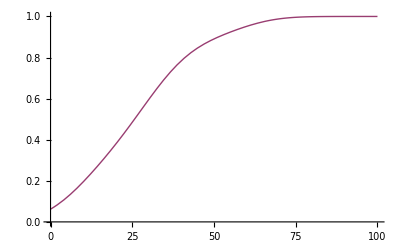

```mathematica
(*generation of Figure 2*)
skddel=SmoothKernelDistribution[Deltas]
Export[$UserDocumentsDirectory<>"\\modelcdf.txt",Deltas,"CSV"]
cdfdel=CDF[skddel,x]

skilldel={6,8,13,25,26,29,35,38,58}
skskilldel=SmoothKernelDistribution[skilldel]
Export[$UserDocumentsDirectory<>"\\skillmancdf.txt",skilldel,"CSV"]
cdfskill=CDF[skskilldel,x]
DistributionFitTest[Deltas,skilldel]

Plot[{cdfdel,cdfskill},{x,0,100}]
```

```mathematica
(*preparation for graphics*)

coskillman=Transpose[{{0,3806,4671,5709,5190,4671},{20,4844,3460,4671,3114,3979}}]
tprskillman=Transpose[{{0,0.0209875,0.0196125,0.01345,0.0163125,0.0160625},{20,0.010075,0.0194125,0.0165625,0.027125,0.018075}}]
Export[$UserDocumentsDirectory<>"\\coskillman.txt",coskillman,"CSV"]
Export[$UserDocumentsDirectory<>"\\tprskillman.txt",tprskillman,"CSV"]

(*CO graph*)
Map[Mean,Transpose[BD[[All,All,2]]]]
Map[StandardDeviation,Transpose[BD[[All,All,2]]]]
Transpose[{Map[Mean,Transpose[BD[[All,All,2]]]],Map[StandardDeviation,Transpose[BD[[All,All,2]]]]}]
Export[$UserDocumentsDirectory<>"\\codata.txt",%,"CSV"]

Print[]
(*TPR graph*)
Map[Mean,Transpose[BD[[All,All,11]]]]
Transpose[{Map[Mean,Transpose[BD[[All,All,11]]]],Map[StandardDeviation,Transpose[BD[[All,All,11]]]]}]
Export[$UserDocumentsDirectory<>"\\tprdata.txt",%,"CSV"]

Print[]
(*TPR graph*)
Map[Mean,Transpose[BD[[All,All,13]]]]
Map[StandardDeviation,Transpose[BD[[All,All,13]]]]

Print[]
(*TPR graph*)
Map[Mean,Transpose[BD[[All,All,33]]]+Transpose[BD[[All,All,36]]]]
Map[StandardDeviation,Transpose[BD[[All,All,33]]]+Transpose[BD[[All,All,36]]]]
```

{{0,20},{3806,4844},{4671,3460},{5709,4671},{5190,3114},{4671,3979}}

{{0,20},{0.0209875,0.010075},{0.0196125,0.0194125},{0.01345,0.0165625},{0.0163125,0.027125},{0.0160625,0.018075}}

C:\Documents and Settings\Hester_lab\My Documents\coskillman.txt

C:\Documents and Settings\Hester_lab\My Documents\tprskillman.txt

{6032.16,5512.19,4973.57,4435.74,3878.98}

{1172.88,1159.9,1246.24,1373.45,1546.8}

{{6032.16,1172.88},{5512.19,1159.9},{4973.57,1246.24},{4435.74,1373.45},{3878.98,1546.8}}

C:\Documents and Settings\Hester_lab\My Documents\codata.txt

{0.0186693,0.0193926,0.0205831,0.0218112,0.0230681}

{{0.0186693,0.00344459},{0.0193926,0.00369357},{0.0205831,0.00449609},{0.0218112,0.00559874},{0.0230681,0.00684365}}

C:\Documents and Settings\Hester_lab\My Documents\tprdata.txt

{1.45191,1.47661,1.53919,1.63745,1.73599}

{0.503786,0.516714,0.552158,0.620906,0.674731}

{2.21017,2.21017,2.21017,2.21017,2.21017}

{0.80457,0.80457,0.80457,0.80457,0.80457}

```mathematica
CorrTable=Table[If[StandardDeviation[AugmentedBD[[All,j]]]>0,Chop[Correlation[AugmentedBD[[All,1]],AugmentedBD[[All,j]]]],0],{j,1,Length[AugmentedBD[[1]]]}];
Players=Select[CorrTable,Abs[#]>0.5&]
CorrReducedPositions=Flatten[Map[Position[CorrTable,#]&,Players]]

TableForm[Transpose[{BleedRoster[[CorrReducedPositions]],CorrTable[[CorrReducedPositions]]}]]
```

{1.,-0.681774,-0.60707,-0.79895,0.52194,-0.88503,-0.757571,-0.885025,-0.776951,-0.675917,0.523128,0.50845,-0.544663,-0.542156}

{1,3,4,5,6,7,8,10,11,13,14,25,41,45}

Delta MAP | 1.
  CardiacOutput.CO | -0.681774
  CardiacOutput.RAP | -0.60707
  CardiacOutput.MCFP | -0.79895
  CardiacOutput.Slope | 0.52194
  FluidVolumes.AP | -0.88503
  FluidVolumes.BV | -0.757571
  FluidVolumes.RPP | -0.885025
  FluidVolumes.UO | -0.776951
  BaroreceptorReflex.AFFNA | -0.675917
  BaroreceptorReflex.SYMEnd | 0.523128
  FluidVolumes.Fluidm | 0.50845
  CardiacOutput.RAP | -0.544663
  FluidVolumes.BV | -0.542156

```mathematica
ClearAll[Players]
DistTable=Table[If[StandardDeviation[DeCompensators[[All,j]]]>0,Chop[DistributionFitTest[Compensators[[All,j]],DeCompensators[[All,j]],Automatic]],1],{j,1,Length[BleedRoster0]}]
CorrTable=Table[If[StandardDeviation[DeCompensators[[All,j]]]>0,Chop[Correlation[AugmentedBD0[[All,j]],AugmentedBD[[All,1]]]],1],{j,1,Length[BleedRoster0]}]
Players=Select[DistTable,Abs[#]<0.05&]
DistReducedPositions=Range[Length[DistTable]];(*Flatten[Map[Position[DistTable,#]&,Players]]*)

DistCompMeans=Map[Mean,Transpose[Compensators[[All,DistReducedPositions]]]];
DistDeCompMeans=Map[Mean,Transpose[DeCompensators[[All,DistReducedPositions]]]];
DistCompSD=Map[StandardDeviation,Transpose[Compensators[[All,DistReducedPositions]]]];
DistDeCompSD=Map[StandardDeviation,Transpose[DeCompensators[[All,DistReducedPositions]]]];
{{"Var","DistFitTest","CorrTable","Comp Means","Comp SD","Decomp Means","Decomp SD"}}
TableForm[Transpose[{BleedRoster0[[DistReducedPositions]],DistTable[[DistReducedPositions]],CorrTable[[DistReducedPositions]],N[DistCompMeans],N[DistCompSD],N[DistDeCompMeans],N[DistDeCompSD]}]]
```

{0,1,0.222541,0,0,0,0,0,5.56567×10^-6,0,0.072434,7.96337×10^-9,0.0020963,0,1,1,1,1,1,0,1,1,1,0.0000167833,1.528×10^-7,1,1,1,1,0.798173,0.00344187,0.00239815,1,0.000201593,2.94647×10^-8,0.00363154,1.62096×10^-8,1,1}

{1.,1,-0.0275596,-0.544663,-0.437916,0.49936,0.473149,-0.542156,-0.186189,0.472939,-0.0241894,0.265451,-0.0643017,0.499636,1,1,1,1,1,-0.279995,1,1,1,0.245492,0.50845,1,1,1,1,0.0366651,-0.0687102,-0.142721,1,-0.221117,-0.385915,0.0509936,0.422062,1,1}

{0,0,0,0,0,0,5.56567×10^-6,0,7.96337×10^-9,0.0020963,0,0,0.0000167833,1.528×10^-7,0.00344187,0.00239815,0.000201593,2.94647×10^-8,0.00363154,1.62096×10^-8}

{{Var,DistFitTest,CorrTable,Comp Means,Comp SD,Decomp Means,Decomp SD}}

Delta MAP | 0 | 1. | 8.48062 | 3.88195 | 41.1936 | 20.6945
  System.X | 1 | 1 | 576000. | 0. | 576000. | 0.
  CardiacOutput.CO | 0.222541 | -0.0275596 | 6181.2 | 1189.84 | 5919.74 | 1150.66
  CardiacOutput.RAP | 0 | -0.544663 | 1.1705 | 2.0323 | -0.864146 | 1.05018
  CardiacOutput.MCFP | 0 | -0.437916 | 8.77805 | 2.11357 | 6.87529 | 1.29098
  CardiacOutput.Slope | 0 | 0.49936 | 0.00747721 | 0.000793513 | 0.00846726 | 0.0012995
  FluidVolumes.AP | 0 | 0.473149 | 104.281 | 6.39866 | 112.633 | 11.6018
  FluidVolumes.BV | 0 | -0.542156 | 4527.62 | 353.728 | 4159.13 | 201.938
  FluidVolumes.ECFV | 5.56567×10^-6 | -0.186189 | 14733.2 | 1635.5 | 13805.4 | 1750.33
  FluidVolumes.RPP | 0 | 0.472939 | 104.283 | 6.40073 | 112.635 | 11.6059
  FluidVolumes.UO | 0.072434 | -0.0241894 | 1.00162 | 0.0856751 | 1.00123 | 0.130349
  FlowAutoregulation.TPR | 7.96337×10^-9 | 0.265451 | 0.017424 | 0.00308603 | 0.0196088 | 0.00341076
  BaroreceptorReflex.AFFNA | 0.0020963 | -0.0643017 | 1.27806 | 0.663084 | 1.10694 | 0.817106
  BaroreceptorReflex.SYMEnd | 0 | 0.499636 | 1.2171 | 0.329223 | 1.62905 | 0.539796
  CardiacOutput.V0 | 1 | 1 | 3330. | 0. | 3330. | 0.
  CardiacOutput.slope_a | 1 | 1 | 0.344 | 0. | 0.344 | 0.
  CardiacOutput.slope_b | 1 | 1 | 0.649 | 0. | 0.649 | 0.
  FluidVolumes.Intake | 1 | 1 | 1. | 0. | 1. | 0.
  FlowAutoregulation.KAUTO | 1 | 1 | 0.00048 | 0. | 0.00048 | 0.
  BaroreceptorReflex.KBARO | 0 | -0.279995 | 0.000983953 | 0.000226752 | 0.000699298 | 0.000405321
  CardiacOutput.StarlingA | 1 | 1 | 7500. | 0. | 7500. | 0.
  CardiacOutput.Starlingm | 1 | 1 | 1.9 | 0. | 1.9 | 0.
  CardiacOutput.StarlingS | 1 | 1 | 2.9 | 0. | 2.9 | 0.
  FluidVolumes.FluidA | 0.0000167833 | 0.245492 | 10111.8 | 1844.95 | 11419.6 | 2989.96
  FluidVolumes.Fluidm | 1.528×10^-7 | 0.50845 | 3.40783 | 1.04998 | 4.3347 | 1.50197
  FluidVolumes.FluidS | 1 | 1 | 15570. | 0. | 15570. | 0.
  FluidVolumes.Urinem | 1 | 1 | 0.05 | 0. | 0.05 | 0.
  FlowAutoregulation.AutoA | 1 | 1 | 0.045 | 0. | 0.045 | 0.
  FlowAutoregulation.Autom | 1 | 1 | 10.86 | 0. | 10.86 | 0.
  FlowAutoregulation.AutoS | 0.798173 | 0.0366651 | 6645. | 1583.25 | 6484.85 | 1523.37
  BaroreceptorReflex.AffNaA | 0.00344187 | -0.0687102 | 2.60728 | 1.30872 | 2.20182 | 1.59327
  BaroreceptorReflex.AffNam | 0.00239815 | -0.142721 | 4.86522 | 1.74726 | 4.13711 | 1.7017
  BaroreceptorReflex.AffNaS | 1 | 1 | 50. | 0. | 50. | 0.
  BaroreceptorReflex.SympsA | 0.000201593 | -0.221117 | 1.20011 | 0.719271 | 0.866754 | 0.562161
  BaroreceptorReflex.Sympsm | 2.94647×10^-8 | -0.385915 | 3.76885 | 1.92437 | 2.64754 | 1.92954
  BaroreceptorReflex.SympsS | 0.00363154 | 0.0509936 | 0.522636 | 0.200501 | 0.531971 | 0.315674
  BaroreceptorReflex.SympsB | 1.62096×10^-8 | 0.422062 | 1.03706 | 0.295252 | 1.32305 | 0.44865
  CardiacOutput.RVRa | 1 | 1 | 0.035 | 0. | 0.035 | 0.
  CardiacOutput.RVRb | 1 | 1 | 0.00064 | 0. | 0.00064 | 0.

{1,3,4,5,6,7,8,10,11,13,14,25}

CardiacOutput.CO

-0.681774

0.222541

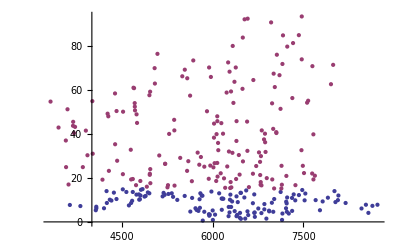

CardiacOutput.RAP

-0.60707

0

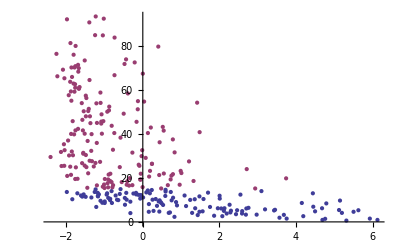

CardiacOutput.MCFP

-0.79895

0

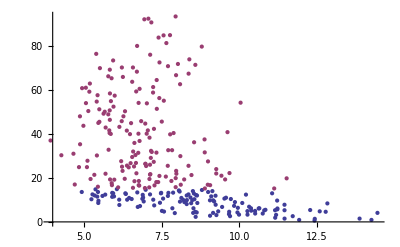

CardiacOutput.Slope

0.52194

0

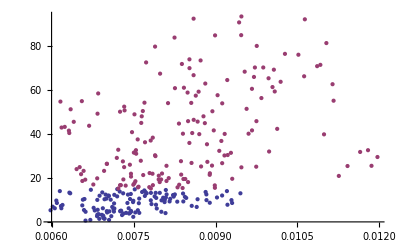

FluidVolumes.AP

-0.88503

0

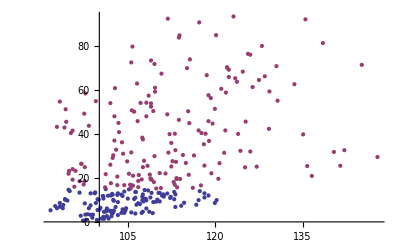

FluidVolumes.BV

-0.757571

0

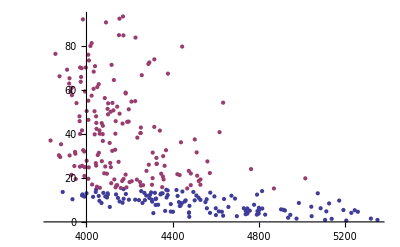

FluidVolumes.RPP

-0.885025

0

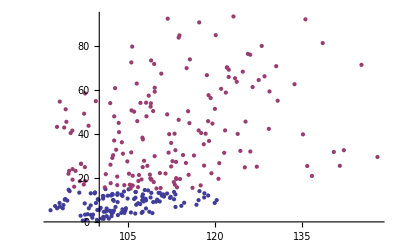

FluidVolumes.UO

-0.776951

0.072434

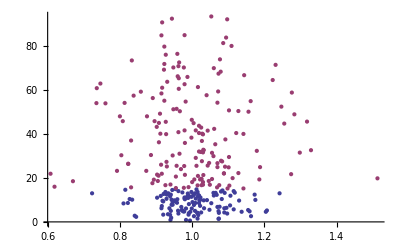

BaroreceptorReflex.AFFNA

-0.675917

0.0020963

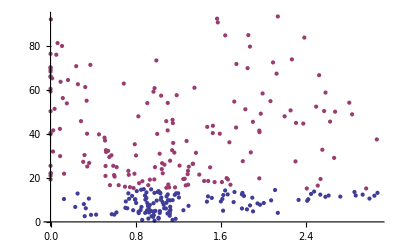

BaroreceptorReflex.SYMEnd

0.523128

0

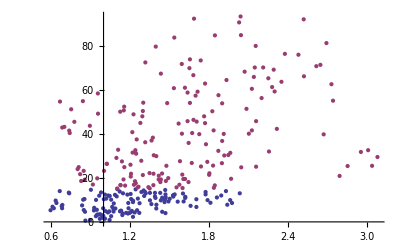

FluidVolumes.Fluidm

0.50845

1.528×10^-7

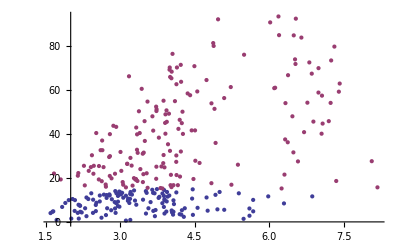

```mathematica
ReducedPositions=Intersection[CorrReducedPositions,DistReducedPositions]
For[j=2,j≤Length[ReducedPositions],
Print[BleedRoster[[ReducedPositions[[j]]]]];
Print[CorrTable[[ReducedPositions[[j]]]]];
Print[DistTable[[ReducedPositions[[j]]]]];
Print[ListPlot[{Transpose[{Compensators[[All,ReducedPositions[[j]]]],Compensators[[All,1]]}],Transpose[{DeCompensators[[All,ReducedPositions[[j]]]],DeCompensators[[All,1]]}]}]];
j++]
```

BaroreceptorReflex.AFFNA

-Graphics-

0.0020963

C:\Documents and Settings\Hester_lab\My Documents\AffNA.txt

BaroreceptorReflex.SYMEnd

-Graphics-

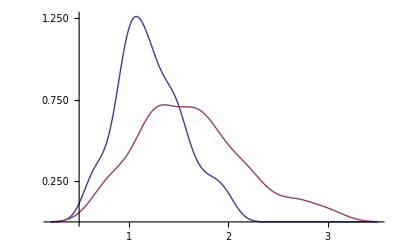

2.20324×10^-12

C:\Documents and Settings\Hester_lab\My Documents\Symps.txt

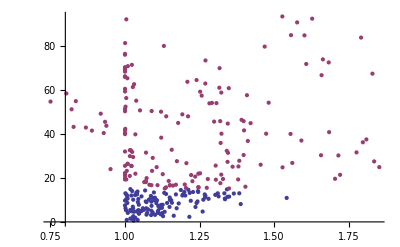

1.12635

1.22948

3.26802×10^-6

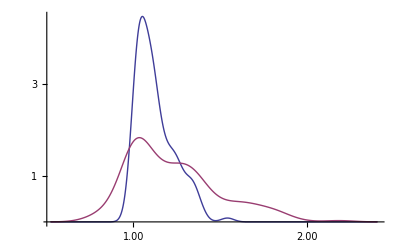

C:\Documents and Settings\Hester_lab\My Documents\Ratio.txt

```mathematica
j=13;
BleedRoster0[[j]]
ListPlot[{Transpose[{Compensators[[All,j]],Compensators[[All,1]]}],Transpose[{DeCompensators[[All,j]],DeCompensators[[All,1]]}]}]
DistributionFitTest[Compensators[[All,j]],DeCompensators[[All,j]]]
Export[$UserDocumentsDirectory<>"\\AffNA.txt",{Compensators[[All,j]],DeCompensators[[All,j]]},"CSV"]
Print[]

j=14;
BleedRoster0[[j]]
ListPlot[{Transpose[{Compensators[[All,j]],Compensators[[All,1]]}],Transpose[{DeCompensators[[All,j]],DeCompensators[[All,1]]}]}]
SmoothHistogram[{Compensators[[All,j]],DeCompensators[[All,j]]}]
DistributionFitTest[Compensators[[All,j]],DeCompensators[[All,j]]]
Export[$UserDocumentsDirectory<>"\\Symps.txt",{Compensators[[All,j]],DeCompensators[[All,j]]},"CSV"]
Print[]

SNARatiosAndLosses=Transpose[{AugmentedBD[[All,14]]/AugmentedBD[[All,51]],AugmentedBD[[All,1]]}];
comp=Select[SNARatiosAndLosses,#[[2]]<=15&];
decomp=Select[SNARatiosAndLosses,#[[2]]>15&];
ListPlot[{comp,decomp}]
Mean[comp[[All,1]]]
Mean[decomp[[All,1]]]
DistributionFitTest[comp[[All,1]],decomp[[All,1]]]
SmoothHistogram[{comp[[All,1]],decomp[[All,1]]}]
Export[$UserDocumentsDirectory<>"\\Ratio.txt",{comp[[All,1]],decomp[[All,1]]},"CSV"]
```

```mathematica
(*Blood data*)
AP0=BD[[All,1,6]];
AP15=BD[[All,4,6]];
AP20=BD[[All,5,6]];
BV0=BD[[All,1,7]];
BV15=BD[[All,4,7]];
BV20=BD[[All,5,7]];
BloodData=Transpose[{AP0-AP15,AP0-AP20,BV0-BV15,BV0-BV20}];
BloodComp15=Select[BloodData,#[[1]]≤15&];
BloodDeComp15=Select[BloodData,#[[1]]>15&];
BloodComp20=Select[BloodData,#[[2]]≤15&];
BloodDeComp20=Select[BloodData,#[[2]]>15&];
Print["Mean blood loss is ",Mean[BloodData[[All,4]]]," ± ",StandardDeviation[BloodData[[All,4]]]]
Print["Mean C20 blood loss is ",Mean[BloodComp20[[All,4]]]," ± ",StandardDeviation[BloodComp20[[All,4]]]]
Print["Mean D15 bloodloss is ",Mean[BloodDeComp15[[All,3]]]," ± ",StandardDeviation[BloodDeComp15[[All,3]]]]
Length[BloodDeComp15]
Print["The distributions are related if p < ",DistributionFitTest[BloodComp20[[All,4]],BloodDeComp15[[All,3]]]]
Print["The correlation between eventual pressure loss and blood loss at 15 minutes is ",Correlation[BloodData[[All,2]],BloodData[[All,3]]]]
```

Mean blood loss is 516.919 ± 198.412

Mean C20 blood loss is 426.071 ± 142.694

Mean D15 bloodloss is 449.019 ± 153.141

134

The distributions are related if p < 0.0201002

The correlation between eventual pressure loss and blood loss at 15 minutes is 0.569474

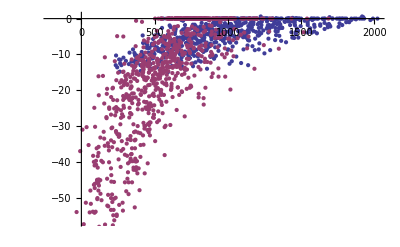

C:\Documents and Settings\Hester_lab\My Documents\PDMCFPComp.txt

C:\Documents and Settings\Hester_lab\My Documents\PDMCFPDeComp.txt

```mathematica
PressureDropsAndMCFP=Flatten[Table[Transpose[{BD[[All,j,7]]-BD[[All,j,14]],BD[[All,j,6]]-BD[[All,1,6]],BD[[All,1,6]]-BD[[All,-1,6]]}],{j,1,5}],1];
PDMCFPComp=Select[PressureDropsAndMCFP,#[[-1]]≤15&];
PDMCFPDeComp=Select[PressureDropsAndMCFP,#[[-1]]>15&];
PDMCFP=ListPlot[{PDMCFPComp[[All,{1,2}]],PDMCFPDeComp[[All,{1,2}]]}]
Export[$UserDocumentsDirectory<>"\\PDMCFPComp.txt",PDMCFPComp,"CSV"]
Export[$UserDocumentsDirectory<>"\\PDMCFPDeComp.txt",PDMCFPDeComp,"CSV"]
```

```mathematica
ReducedPositions={4,6,7,14}

j=1;
Export[$UserDocumentsDirectory<>"\\RAPComp.txt",Transpose[{Compensators[[All,ReducedPositions[[j]]]],Compensators[[All,1]]}],"CSV"];
Export[$UserDocumentsDirectory<>"\\RAPDeComp.txt",Transpose[{DeCompensators[[All,ReducedPositions[[j]]]],DeCompensators[[All,1]]}],"CSV"]

j=2;
Export[$UserDocumentsDirectory<>"\\SlopComp.txt",Transpose[{Compensators[[All,ReducedPositions[[j]]]],Compensators[[All,1]]}],"CSV"];
Export[$UserDocumentsDirectory<>"\\SlopeDeComp.txt",Transpose[{DeCompensators[[All,ReducedPositions[[j]]]],DeCompensators[[All,1]]}],"CSV"]

j=3;
Export[$UserDocumentsDirectory<>"\\APComp.txt",Transpose[{Compensators[[All,ReducedPositions[[j]]]],Compensators[[All,1]]}],"CSV"];
Export[$UserDocumentsDirectory<>"\\APDeComp.txt",Transpose[{DeCompensators[[All,ReducedPositions[[j]]]],DeCompensators[[All,1]]}],"CSV"]

j=4;
Export[$UserDocumentsDirectory<>"\\SymComp.txt",Transpose[{Compensators[[All,ReducedPositions[[j]]]],Compensators[[All,1]]}],"CSV"];
Export[$UserDocumentsDirectory<>"\\SymDeComp.txt",Transpose[{DeCompensators[[All,ReducedPositions[[j]]]],DeCompensators[[All,1]]}],"CSV"]
```

{4,6,7,14}

C:\Documents and Settings\Hester_lab\My Documents\RAPDeComp.txt

C:\Documents and Settings\Hester_lab\My Documents\SlopeDeComp.txt

C:\Documents and Settings\Hester_lab\My Documents\APDeComp.txt

C:\Documents and Settings\Hester_lab\My Documents\SymDeComp.txt

{19,23,24,29,30,31,33,34,35,36}

```mathematica
(*Blood data*)
AP0=BD[[All,1,6]];
AP10=BD[[All,3,6]];
AP15=BD[[All,4,6]];
AP20=BD[[All,5,6]];
BV0=BD[[All,1,7]];
BV10=BD[[All,3,7]];
BV15=BD[[All,4,7]];
BV20=BD[[All,5,7]];
BloodData=Transpose[{AP0-AP15,AP0-AP20,BV0-BV15,BV0-BV20,AP0-AP10,BV0-BV10}];
BloodComp10=Select[BloodData,#[[5]]≤15&];
BloodDeComp10=Select[BloodData,#[[5]]>15&];
BloodComp15=Select[BloodData,#[[1]]≤15&];
BloodDeComp15=Select[BloodData,#[[1]]>15&];
BloodComp20=Select[BloodData,#[[2]]≤15&];
BloodDeComp20=Select[BloodData,#[[2]]>15&];
Print["Mean blood loss is ",Mean[BloodData[[All,4]]]," ± ",StandardDeviation[BloodData[[All,4]]]]
Print["Mean C20 blood loss is ",Mean[BloodComp20[[All,4]]]," ± ",StandardDeviation[BloodComp20[[All,4]]]]
Print["Mean D15 bloodloss is ",Mean[BloodDeComp15[[All,3]]]," ± ",StandardDeviation[BloodDeComp15[[All,3]]]]
Length[BloodDeComp15]

Print["The distributions are related if p < ",DistributionFitTest[BloodComp20[[All,4]],BloodDeComp15[[All,3]]]]
Print["The correlation between eventual pressure loss and blood loss at 15 minutes is ",Correlation[BloodData[[All,2]],BloodData[[All,3]]]]
Print["Percent Blood loss at 10 minutes is ",375/Mean[BD[[All,1,7]]]]
Print["Percent Blood loss at 15 minutes is ",(37.5*15)/Mean[BD[[All,1,7]]]]
Print["Mean D10 bloodloss is ",Mean[BloodDeComp10[[All,3]]]," ± ",StandardDeviation[BloodDeComp10[[All,3]]]]
N[Length[BloodDeComp10]/(Length[BloodDeComp10]+Length[BloodComp10])]
```

Mean blood loss is 516.919 ± 198.412

Mean C20 blood loss is 426.071 ± 142.694

Mean D15 bloodloss is 449.019 ± 153.141

134

The distributions are related if p < 0.0201002

The correlation between eventual pressure loss and blood loss at 15 minutes is 0.569474

Percent Blood loss at 10 minutes is 0.0868542

Percent Blood loss at 15 minutes is 0.130281

Mean D10 bloodloss is 452.718 ± 119.1

0.28

```mathematica
BleedDataForSVM=ToExpression[Import[pathdata<>"Middle.CSV"]]
```

{{{{BleedDataForSVM}}}}

```mathematica
BD=ToExpression[Import["C:\\Documents and Settings\\Hester_lab\\Desktop\\BleedDataBest.txt","List"]];
```

```mathematica
Head[ToExpression[BD[[1]]][[1,1]]]
```

Real

```mathematica
Export["C:\\Documents and Settings\\Hester_lab\\Desktop\\"<>"Deltas.xlsx",Deltas]
```

C:\Documents and Settings\Hester_lab\Desktop\Deltas.xlsx